```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sasaki/Dropbox/@Res-SHARED/@OLIGOMORPH/Antigenic Escape and virulence/Antigen Escape and Virulence Evolution/Manusripts/-Source codes for figures/Figure 5

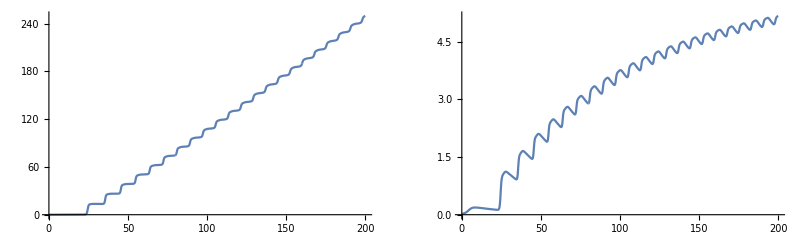

```mathematica
datMoments=ReadList["sim_data/mean.d",Number,RecordLists->True];
{tmMom,ItMom,exMom,eαMom,vxxMom,vααMom, vxαMom}=Transpose[datMoments];
GraphicsRow[{ListLinePlot[Transpose[{tmMom,exMom}],ImageSize->200],ListLinePlot[Transpose[{tmMom,eαMom}],ImageSize->200]}]
```

```mathematica
datMarX=ReadList["sim_data/marginal-x.d",Number,RecordLists->True];
{tMar,xMar,IxMar}=Transpose[datMarX];
tMar=Union[tMar];xMar=Union[xMar];IxMar=Partition[IxMar,Length[xMar]];
ListContourPlot[Transpose[IxMar^0.2],ColorFunction->(GrayLevel[1-#]&),DataRange->{{Min[tMar],Max[tMar]},{Min[xMar],Max[xMar]}},ImageSize->250,FrameLabel->{"t","x"}]
```

-Graphics-

```mathematica
datMarA=ReadList["sim_data/marginal-a.d",Number,RecordLists->True];
{tMar,aMar,IaMar}=Transpose[datMarA];
tMar=Union[tMar];aMar=Union[aMar];IaMar=Partition[IaMar,Length[aMar]];
ListContourPlot[Transpose[IaMar^0.2],ColorFunction->(GrayLevel[1-#]&),DataRange->{{Min[tMar],Max[tMar]},{Min[aMar],Max[aMar]}},ImageSize->250,FrameLabel->{"t","α"},PlotRange->All]
```

-Graphics-

```mathematica
ϕaMar=Table[IaMar⟦i⟧/Total[IaMar⟦i⟧],{i,Length[IaMar]}];
ListContourPlot[Transpose[ϕaMar],ColorFunction->(GrayLevel[1-#]&),DataRange->{{Min[tMar],Max[tMar]},{Min[aMar],Max[aMar]}},ImageSize->250,FrameLabel->{"t","α"},PlotRange->{0,0.2}]
```

-Graphics-

```mathematica
datJoint=ReadList["sim_data/joint.d",Number,RecordLists->True];
{timeJoint,xJoint,αJoint,ϕJoint}=Transpose[datJoint];
timeJoint=Union[timeJoint];
xJoint=Union[xJoint];
αJoint=Union[αJoint];
```

```mathematica
Clear[JointDistribution]
JointDistribution[id_,data_,sigma_,{xmin_,xmax_},{amin_,amax_}]:=Module[{da,t,x,alf,phi},
da=Select[data,#⟦1⟧==timeJoint⟦id⟧&];
{t,x,alf,phi}=Transpose[da];
x=Union[x];
alf=Union[alf];
phi=Partition[phi,Length[alf]];

ListContourPlot[Transpose[phi^sigma],ColorFunction->(GrayLevel[(1-#)]&),PlotLegends->Automatic,PlotRange->{{xmin,xmax},{amin,amax},All},DataRange->{{Min[x],Max[x]},{Min[alf],Max[alf]}},FrameLabel->{"x","α"},ImageSize->250,PlotLabel->"time = "<>ToString[timeJoint⟦id⟧]]
]
JointDistributionNoLegends[id_,data_,sigma_,{xmin_,xmax_},{amin_,amax_}]:=Module[{da,t,x,alf,phi},
da=Select[data,#⟦1⟧==timeJoint⟦id⟧&];
{t,x,alf,phi}=Transpose[da];
x=Union[x];
alf=Union[alf];
phi=Partition[phi,Length[alf]];

ListContourPlot[Transpose[phi^sigma],ColorFunction->(GrayLevel[(1-#)]&),PlotRange->{{xmin,xmax},{amin,amax},All},DataRange->{{Min[x],Max[x]},{Min[alf],Max[alf]}},FrameLabel->{"x","α"},ImageSize->250,PlotLabel->"time = "<>ToString[timeJoint⟦id⟧]]
]
```

```mathematica
JointDistribution[1,datJoint,0.2,{100,120},{2,6}]
JointDistribution[Length[timeJoint],datJoint,0.2,{100,150},{2,6}]
```

-Graphics-

-Graphics-

```mathematica
Length[time]
```

0

```mathematica
JointDistribution[1,datJoint,0.2,{90,120},{2,6}]
```

-Graphics-

```mathematica
Do[JointDistribution[id,datJoint,0.5,{100,130},{2,6}]//Print,{id,100,250,10}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

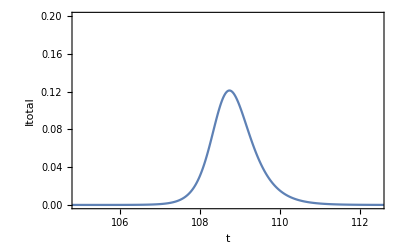

```mathematica
ListLinePlot[Transpose[{tmMom,ItMom}],PlotRange->{{timeJoint⟦100⟧,timeJoint⟦250⟧},{0,0.2}},Frame->True,FrameLabel->{"t","Itotal"}]
```

```mathematica
Clear[Moments]
Moments[id_,data_]:=Module[{da,t,x,alf,phi,Ex,Eα,ξ,ζ,Vxx,Vxα,Vαα},
da=Select[data,#⟦1⟧==timeJoint⟦id⟧&];
{t,x,alf,phi}=Transpose[da];
Ex=x.phi;
Eα=alf.phi;
ξ=x-Ex;
ζ=alf-Eα;
Vxx=(ξ^2).phi;
Vxα=(ξ ζ).phi;
Vαα=(ζ^2).phi;
{Ex,Eα,Vxx,Vxα,Vαα}
]
```

```mathematica
(* moments=Table[(If[Mod[i,20]==0,Print[i]];Moments[i,data]),{i,Length[time]}];
*)
```

```mathematica
Moments[1,datJoint]
```

{107.687,3.75808,1.06575,0.0453667,0.0863843}

```mathematica
tmin=Min[timeJoint];
tmax=Max[timeJoint];
datMomSelect=Select[datMoments,(#⟦1⟧≥tmin&&#⟦1⟧≤tmax)&];
{tm,It,ex,ea,vxx,vαα, vxα}=Transpose[datMomSelect];
```

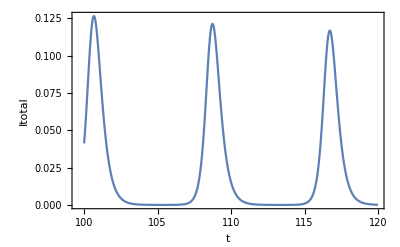

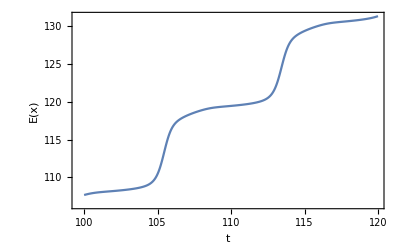

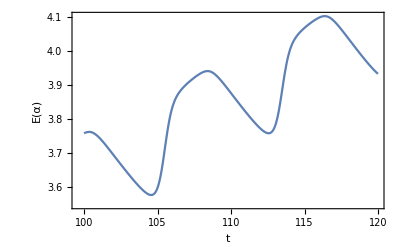

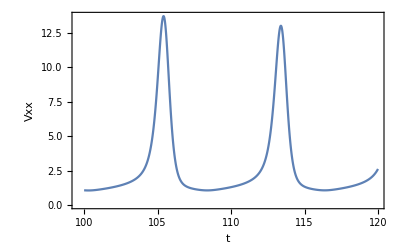

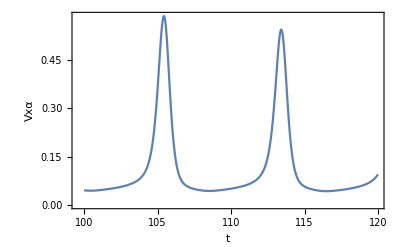

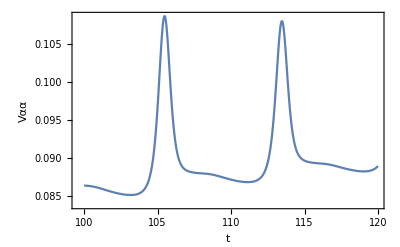

```mathematica
ListLinePlot[Transpose[{tm,It}],Frame->True,FrameLabel->{"t","Itotal"}]
ListLinePlot[Transpose[{tm,ex}],Frame->True,FrameLabel->{"t","E(x)"}]
ListLinePlot[Transpose[{tm,ea}],Frame->True,FrameLabel->{"t","E(α)"}]
ListLinePlot[Transpose[{tm,vxx}],Frame->True,FrameLabel->{"t","Vxx"},PlotRange->All]
ListLinePlot[Transpose[{tm,vxα}],Frame->True,FrameLabel->{"t","Vxα"},PlotRange->All]
ListLinePlot[Transpose[{tm,vαα}],Frame->True,FrameLabel->{"t","Vαα"},PlotRange->All]
```

## OMD prediction from around t = 105

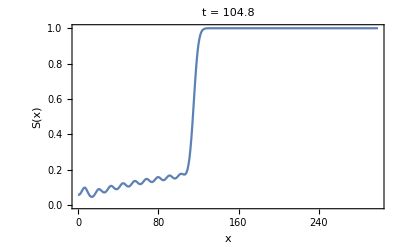

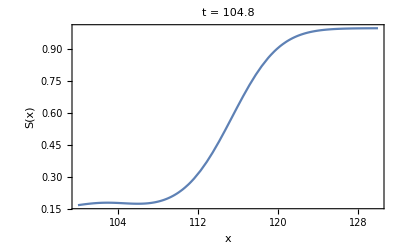

```mathematica
datSProf=ReadList["sim_data/susceptibility.d",Number,RecordLists->True];
{tSProf,xProf,sProf}=Transpose[datSProf];
tSProf=Union[tSProf];

idA=263;
da=Select[datSProf,#⟦1⟧==tSProf⟦idA⟧&];
{dum,xx,ss}=Transpose[da];
ListLinePlot[Transpose[{xx,ss}],Frame->True,FrameLabel->{"x","S(x)"},PlotLabel->"t = "<>ToString[tSProf⟦idA⟧]]

daa=Select[da,(#⟦2⟧≥100&&#⟦2⟧≤130)&];
{dum,xx,ss}=Transpose[daa];

Clear[S]
S=Interpolation[Transpose[{xx,ss}]];
Plot[S[x],{x,100,130},Frame->True,FrameLabel->{"x","S(x)"},PlotLabel->"t = "<>ToString[tSProf⟦idA⟧]]
```

```mathematica
idB=97;
JointDistribution[idB,datJoint,0.5,{100,130},{2,6}]
```

-Graphics-

5 √α

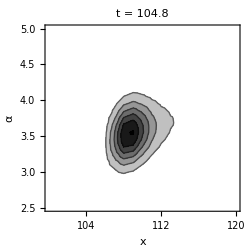

{109.775,3.58203,6.37821,0.24762,0.0917504}

```mathematica
CONST=5;
β[α_]=CONST Sqrt[α]
γ=0.5;
idB=97;
da=Select[datJoint,#⟦1⟧==timeJoint⟦idB⟧&];
{t,x,alf,phi}=Transpose[da];
x=Union[x];
alf=Union[alf];
phi=Partition[phi,Length[alf]];

ListContourPlot[Transpose[phi],PlotRange->{{100,120},{2.5,5},All},ColorFunction->(GrayLevel[1-#]&),DataRange->{{Min[x],Max[x]},{Min[alf],Max[alf]}},ImageSize->250,FrameLabel->{"x","α"},PlotLabel->"t = "<>ToString[timeJoint⟦idB⟧]]

{Ex,Eα,Vxx,Vxα,Vαα}=Moments[idB,datJoint]
```

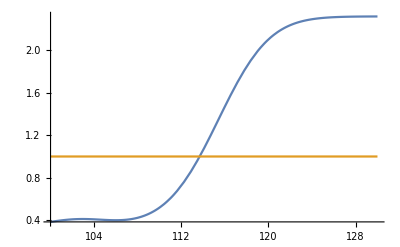

113.684

```mathematica
Plot[{(β[Eα]S[x])/(γ+Eα),1},{x,100,130}]
Clear[x]
xc=x/.FindRoot[(β[Eα]S[x])/(γ+Eα)==1,{x,110}]
```

```mathematica
Show[
JointDistribution[idB,datJoint,0.5,{100,120},{2.5,5}],
Graphics[{Red,Dashed,Line[{{xc,2.5},{xc,5}}]}]
]
```

-Graphics-

```mathematica
Clear[MomentsUD]
MomentsUD[id_,data_,xc_]:=Module[{da,daU,daD,t,x,alf,phi,p,Ex,Eα,ξ,ζ,resU,resD},
da=Select[data,#⟦1⟧==timeJoint⟦id⟧&];
daU=Select[da,(#⟦2⟧>xc)&];
daD=Select[da,(#⟦2⟧≤ xc)&];
{t,x,alf,phi}=Transpose[daU];
p=Total[phi];
phi=phi/p;
{Ex,Eα}={x.phi,alf.phi};
{ξ,ζ}={x-Ex,alf-Eα};
resU={p,Ex,Eα,(ξ^2).phi,(ξ ζ).phi,(ζ^2).phi};

{t,x,alf,phi}=Transpose[daD];
p=Total[phi];
phi=phi/p;
{Ex,Eα}={x.phi,alf.phi};
{ξ,ζ}={x-Ex,alf-Eα};
resD={p,Ex,Eα,(ξ^2).phi,(ξ ζ).phi,(ζ^2).phi};
{resU,resD}
]
```

```mathematica
MomentsUD[idB,datJoint,xc]
{RESU,RESD}=%;
```

{{0.104655,115.374,3.79968,1.53722,0.0622633,0.0869899},{0.895333,109.122,3.55663,2.85283,0.110251,0.0861259}}

```mathematica
fp=β[α]S[x]-α;
Fx=D[β[α]S[x]-α,x];
Fα=D[β[α]S[x]-α,α];
Hxx=D[β[α]S[x]-α,{x,2}];
Hxα=D[D[β[α]S[x]-α,x],α];
Hαα=D[β[α]S[x]-α,{α,2}];
```

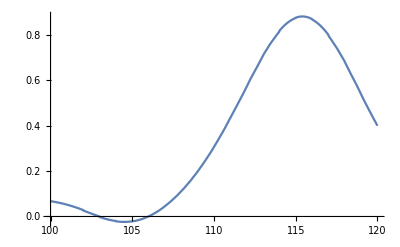

```mathematica
Plot[Fx/.α->3.8,{x,100,120}]
```

### OMD

```mathematica
{pU0,ExU0,EαU0,VxxU0,VxαU0,VααU0}=RESU
{pD0,ExD0,EαD0,VxxD0,VxαD0,VααD0}=RESD
```

{0.104655,115.374,3.79968,1.53722,0.0622633,0.0869899}

{0.895333,109.122,3.55663,2.85283,0.110251,0.0861259}

```mathematica
Clear[ExU,EαU,VxxU,VxαU,VααU,t]
{fpU,FxU,FαU,HxxU,HxαU,HααU}=Evaluate[{fp,Fx,Fα,Hxx,Hxα,Hαα}/.{α->EαU[t],x->ExU[t]}];
Clear[ExD,EαD,VxxD,VxαD,VααD]
{fpD,FxD,FαD,HxxD,HxαD,HααD}=Evaluate[{fp,Fx,Fα,Hxx,Hxα,Hαα}/.{α->EαD[t],x->ExD[t]}];
```

104.8

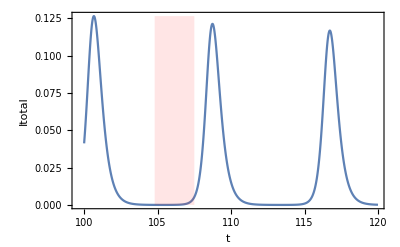

```mathematica
t0=timeJoint⟦idB⟧
(* te=109; *)
te=107.5;
itmax=Max[It];
ListLinePlot[Transpose[{tm,It}],Frame->True,FrameLabel->{"t","Itotal"},Epilog->{Red,Opacity[0.1],Rectangle[{t0,0},{te,itmax}]}]
```

```mathematica
Position[tm,te]
```

{{751}}

```mathematica
Position[tm,107.]
```

{{701}}

{99.4548,3.40958}

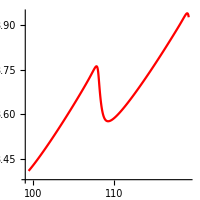

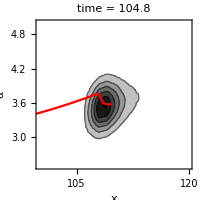

```mathematica
{{i0}}=Position[tmMom,97.];
{Part[exMom,i0],Part[eαMom,i0]}
{{is}}=Position[tmMom,104.8];
{{im}}=Position[tmMom,107.];
{{ie}}=Position[tmMom,109.];
Show[
ListLinePlot[Take[Transpose[{exMom,eαMom}],{i0,ie}],PlotStyle->Red],ImageSize->200,AspectRatio->1
]
xrange={100,120};
αrange={2.5,5};
Show[
JointDistributionNoLegends[idB,datJoint,1.0,xrange,αrange],
ListLinePlot[Take[Transpose[{exMom,eαMom}],{i0,is}],PlotStyle->{Red}],ImageSize->200
]
```

```mathematica
Part[exMom,is]
```

109.776

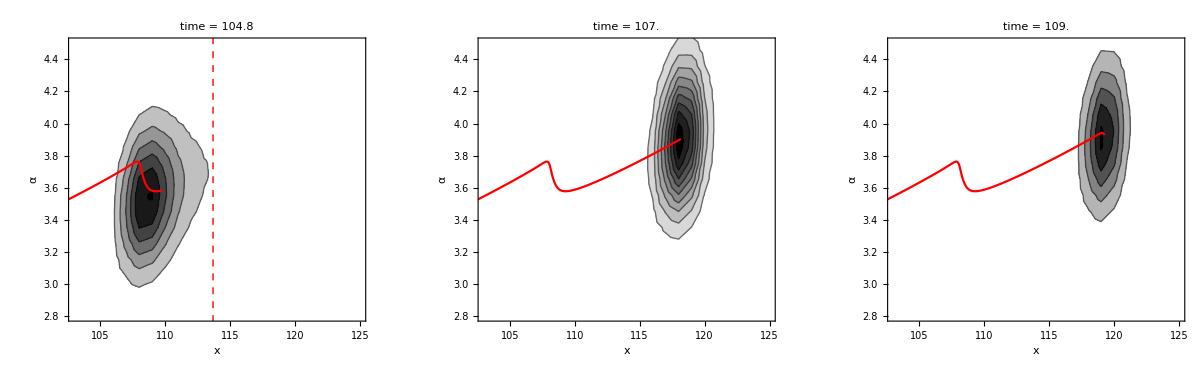

```mathematica
xrange={103,125};
arange={2.8,4.5};
figA=Show[
JointDistributionNoLegends[idB,datJoint,1.0,xrange,arange],
{{ip}}=Position[tmMom,97.];
{{is}}=Position[tmMom,t0];
ListLinePlot[Take[Transpose[{exMom,eαMom}],{ip,is}],PlotStyle->{Red}],
Graphics[{Red,Dashed,Line[{{xc,2.5},{xc,5}}]}],ImageSize->200
];
figB=Show[
id=idB+44;
{{im}}=Position[tmMom,timeJoint⟦id⟧];
JointDistributionNoLegends[id,datJoint,1.0,xrange,arange],
ListLinePlot[Take[Transpose[{exMom,eαMom}],{ip,im}],PlotStyle->{Red}],
ImageSize->200];
figC=Show[
id=idB+84;
{{ie}}=Position[tmMom,timeJoint⟦id⟧];
JointDistributionNoLegends[id,datJoint,1.0,xrange,arange],
ListLinePlot[Take[Transpose[{exMom,eαMom}],{ip,ie}],PlotStyle->{Red}],ImageSize->200];
GraphicsRow[{figA,figB,figC}]
```

```mathematica
Clear[flowU]
𝒟x=0.005;
𝒟α=0.0002;
flowU={
PU'[t]==(fpU-fpD)PU[t](1-PU[t]),
ExU'[t]==FxU VxxU[t]+FαU VxαU[t],
EαU'[t]==FxU VxαU[t]+FαU VααU[t],
VxxU'[t]==
HxxU (VxxU[t])^2+
2HxαU VxxU[t]VxαU[t]+
HααU (VxαU[t])^2+2𝒟x,
VxαU'[t]==
HxxU VxxU[t]VxαU[t]+HxαU(VxxU[t]VααU[t]+(VxαU[t])^2)+HααU VxαU[t]VααU[t],
VααU'[t]==
HααU (VααU[t])^2+
2HxαU VααU[t]VxαU[t]+
HxxU (VxαU[t])^2+2𝒟α,

ExD'[t]==FxD VxxD[t]+FαD VxαD[t],
EαD'[t]==FxD VxαD[t]+FαD VααD[t],
VxxD'[t]==
HxxD (VxxD[t])^2+
2HxαD VxxD[t]VxαD[t]+
HααD (VxαD[t])^2+2𝒟x,
VxαD'[t]==
HxxD VxxD[t]VxαD[t]+HxαD(VxxD[t]VααD[t]+(VxαD[t])^2)+HααD VxαD[t]VααD[t],
VααD'[t]==
HααD (VααD[t])^2+
2HxαD VααD[t]VxαD[t]+
HxxD (VxαD[t])^2+2𝒟α,

PU[t0]==pU0,
ExU[t0]==ExU0,
EαU[t0]==EαU0,
VxxU[t0]==VxxU0,
VxαU[t0]==VxαU0,
VααU[t0]==VααU0,

ExD[t0]==ExD0,
EαD[t0]==EαD0,
VxxD[t0]==VxxD0,
VxαD[t0]==VxαD0,
VααD[t0]==VααD0};
ser=NDSolve[flowU,{PU,ExU,EαU,VxxU,VxαU,VααU,ExD,EαD,VxxD,VxαD,VααD},{t,t0,te}];
```

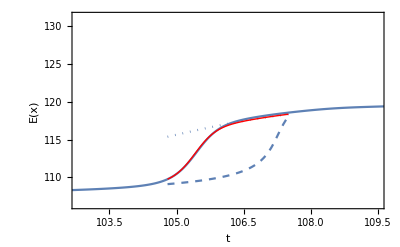

```mathematica
Show[
ListLinePlot[Transpose[{tm,ex}],PlotRange->{{t0-2,te+2},All},Frame->True,FrameLabel->{"t","E(x)"}],
Plot[ExU[t]/.ser,{t,t0,te},PlotStyle->{Dotted}],
Plot[ExD[t]/.ser,{t,t0,te},PlotStyle->{Dashed}],
Plot[(1-PU[t])ExD[t]+PU[t]ExU[t]/.ser,{t,t0,te},PlotStyle->{Red,Thick}]
]
```

```mathematica
trange={t0-2,te+6};
```

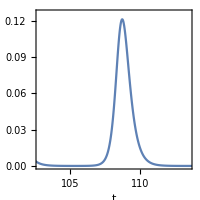

```mathematica
figD=ListLinePlot[Transpose[{tm,It}],PlotRange->{trange,All},Frame->True,FrameLabel->{"t","Itotal"},ImageSize->200,AspectRatio->1]
```

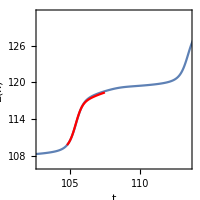

```mathematica
figE=Show[
ListLinePlot[Transpose[{tm,ex}],PlotRange->{trange,All},Frame->True,FrameLabel->{"t","E(x)"},ImageSize->200,AspectRatio->1],
Plot[(1-PU[t])ExD[t]+PU[t]ExU[t]/.ser,{t,t0,te},PlotStyle->Red]
]
```

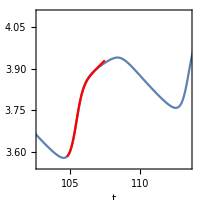

```mathematica
figF=Show[
ListLinePlot[Transpose[{tm,ea}],PlotRange->{trange,All},Frame->True,FrameLabel->{"t","E(α)"},ImageSize->200,AspectRatio->1],
Plot[(1-PU[t])EαD[t]+PU[t]EαU[t]/.ser,{t,t0,te},PlotStyle->Red]
]
```

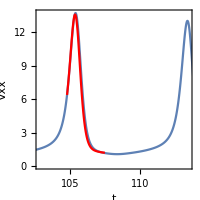

```mathematica
figG=Show[
ListLinePlot[Transpose[{tm,vxx}],PlotRange->{trange,All},Frame->True,FrameLabel->{"t","Vxx"},ImageSize->200,AspectRatio->1],
Plot[(1-PU[t])VxxD[t]+PU[t]VxxU[t]+PU[t](1-PU[t])(ExU[t]-ExD[t])^2/.ser,{t,t0,te},PlotStyle->Red,PlotRange->All]
]
```

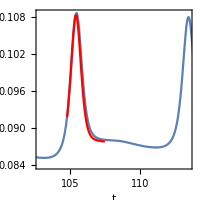

```mathematica
figH=Show[
ListLinePlot[Transpose[{tm,vαα}],PlotRange->{trange,All},Frame->True,FrameLabel->{"t","Vαα"},ImageSize->200,AspectRatio->1],
Plot[(1-PU[t])VααD[t]+PU[t]VααU[t]+PU[t](1-PU[t])(EαU[t]-EαD[t])^2/.ser,{t,t0,te},PlotStyle->Red,PlotRange->All]
]
```

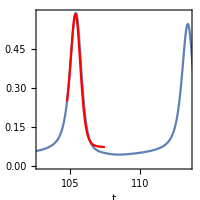

```mathematica
figI=Show[
ListLinePlot[Transpose[{tm,vxα}],PlotRange->{trange,All},Frame->True,FrameLabel->{"t","Vxα"},ImageSize->200,AspectRatio->1],
Plot[(1-PU[t])VxαD[t]+PU[t]VxαU[t]+PU[t](1-PU[t])(ExU[t]-ExD[t])(EαU[t]-EαD[t])/.ser,{t,t0,te},PlotStyle->Red,PlotRange->All]
]
```

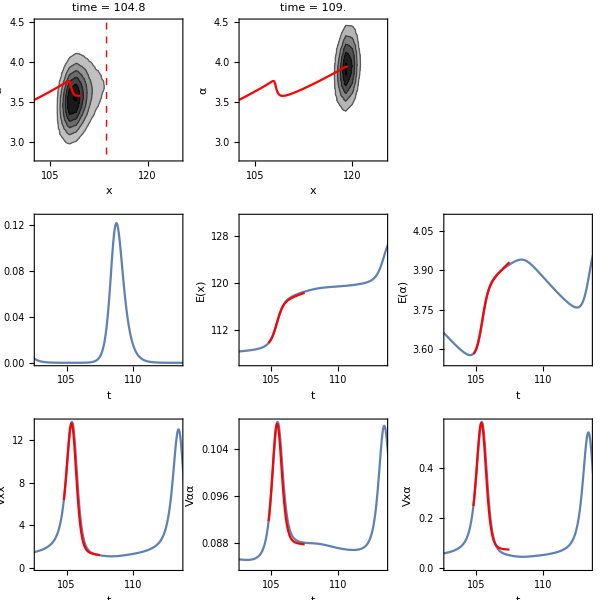

```mathematica
fig=GraphicsGrid[{{figA,figC,Null},{figD,figE,figF},{figG,figH,figI}},ImageSize->600]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["fig/OMD_JointEvolution.eps",fig]
Export["fig/OMD_JointEvolution.pdf",fig]
```

/Users/sasaki/Dropbox/@Res-SHARED/@OLIGOMORPH/Antigenic Escape and virulence/Antigen Escape and Virulence Evolution/Manusripts/-Source codes for figures/Figure 5

fig/OMD_JointEvolution.eps

fig/OMD_JointEvolution.pdf

```mathematica
Clear[dG]
dG[G_,H_]:=Table[
Sum[G⟦i,k⟧H⟦k,l⟧G⟦l,j⟧,{k,2},{l,2}],{i,2},{j,2}]
```

```mathematica
Clear[Vxx,G,H]
G={{Vxx,Cxy},{Cxy,Vyy}};
H={{Wxx,Wxy},{Wxy,Wyy}};
```

```mathematica
dG[G,H]
```

{{Vxx^2 Wxx+2 Cxy Vxx Wxy+Cxy^2 Wyy,Cxy Vxx Wxx+Cxy^2 Wxy+Vxx Vyy Wxy+Cxy Vyy Wyy},{Cxy Vxx Wxx+Cxy^2 Wxy+Vxx Vyy Wxy+Cxy Vyy Wyy,Cxy^2 Wxx+2 Cxy Vyy Wxy+Vyy^2 Wyy}}

```mathematica
dG[G,H]⟦1,1⟧//Collect[#,{Wxx,Wxy,Wyy},Simplify]&
dG[G,H]⟦1,2⟧//Collect[#,{Wxx,Wxy,Wyy},Simplify]&
dG[G,H]⟦2,1⟧//Collect[#,{Wxx,Wxy,Wyy},Simplify]&
dG[G,H]⟦2,2⟧//Collect[#,{Wxx,Wxy,Wyy},Simplify]&
```

Vxx^2 Wxx+2 Cxy Vxx Wxy+Cxy^2 Wyy

Cxy Vxx Wxx+(Cxy^2+Vxx Vyy) Wxy+Cxy Vyy Wyy

Cxy Vxx Wxx+(Cxy^2+Vxx Vyy) Wxy+Cxy Vyy Wyy

Cxy^2 Wxx+2 Cxy Vyy Wxy+Vyy^2 Wyy